```mathematica
Clear["Global`*"]
$Assumptions=True;
```

Dim initial value problem (ivp):

```mathematica
mdl={deqn=c'[t]==-c[t], iv=c[0]==1};
```

```mathematica
$Assumptions=c[t]>0&&t>0;
```

Solution:

Find the scale factors and replace them into the model:

```mathematica
sln=DSolve[mdl,c[t],t]
```

{{c[t]→ⅇ^-t}}

Get the solution and assign it to c:

```mathematica
c[t_]=c[t]/.sln[[1]]//FullSimplify
```

ⅇ^-t

Verify that the solution satisfies the ivp:

```mathematica
deqn//FullSimplify
```

True

```mathematica
iv//FullSimplify
```

True

Find limits:

```mathematica
Limit[c[t],t->0]
```

1

```mathematica
Limit[c[t],t->Infinity]
```

0

Find the value for which c is nul:

```mathematica
Solve[c[t]==0,t]
```

{}

Find the dimless halflife time (time for which c is 1/2) (working in dimless mode, remember?):

```mathematica
th=Solve[c[t]==1/2,t, Reals]
```

{{t→Log[2]}}

```mathematica
c[th]//FullSimplify
```

{{ⅇ^(-(t→Log[2]))}}

(With the value of th, a new time scale can be found.)

Find the max and min:

```mathematica
FindMaximum[c[t],t]
```

General::ovfl: Overflow occurred in computation.

FindMaximum::nrnum: The function value Overflow[] is not a real number at {t} = {-7.595×10^15}.

{7.8646271519284410037349960327970786143`15.954589770191005*^299860467688871,{t→-6.90454×10^14}}

```mathematica
FindMinimum[c[t],t]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{4.11428×10^-31,{t→69.9657}}

Plot the solution:

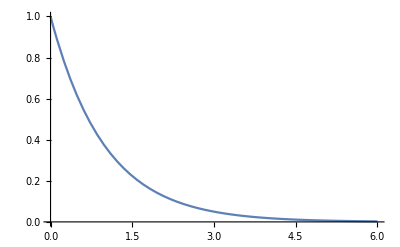

```mathematica
Plot[c[t],{t,0,6},PlotRange->{0,1}]
```